```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\GitHub\VM2D\settings\airfoils

```mathematica
h=0.33
```

0.33

```mathematica
sp=33
```

33

```mathematica
n=800;
```

```mathematica
L=33/n;
```

```mathematica
nc=Ceiling[(π h)/L/4]*4
```

28

```mathematica
Larc=π h/2 /nc
```

0.018513

```mathematica
nr=Ceiling[(sp-h)/Larc]
```

1765

```mathematica
(sp-h)/nr
```

0.0185099

```mathematica
PtsA=N[Table[{(sp/2-h/2)+h/2 Cos[-π/2+(2π)/nc(i-1.0)],h/2 Sin[-π/2+(2π)/nc(i-1.0)]},{i,1,nc/2+1}],16]
```

{{16.335,-0.165},{16.3717,-0.160863},{16.4066,-0.14866},{16.4379,-0.129002},{16.464,-0.102876},{16.4837,-0.0715908},{16.4959,-0.036716},{16.5,0.},{16.4959,0.036716},{16.4837,0.0715908},{16.464,0.102876},{16.4379,0.129002},{16.4066,0.14866},{16.3717,0.160863},{16.335,0.165}}

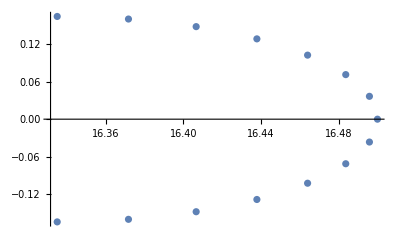

```mathematica
ListPlot[PtsA]
```

```mathematica
PtsB=Table[{sp/2-h/2-(sp-h)/nr(i-1),h/2},{i,2,nr-1}];
```

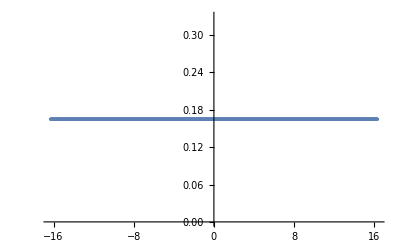

```mathematica
ListPlot[PtsB]
```

```mathematica
PtsC=N[Table[{(-sp/2+h/2)+h/2 Cos[π/2+(2π)/nc(i-1.0)],h/2 Sin[π/2+(2π)/nc(i-1.0)]},{i,1,nc/2+1}],16];
```

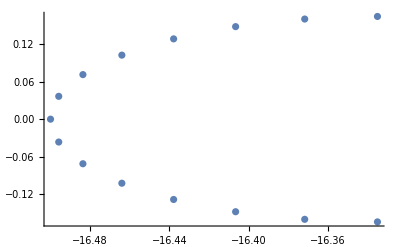

```mathematica
ListPlot[PtsC]
```

```mathematica
PtsD=Table[{-sp/2+h/2+(sp-h)/nr(i-1),-h/2},{i,2,nr-1}];
```

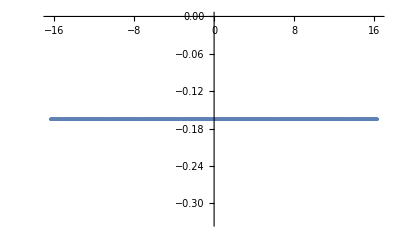

```mathematica
ListPlot[PtsD]
```

```mathematica
PtsA[[1]]
```

{16.335,-0.165}

```mathematica
Pts=RotateLeft[Join[PtsA,PtsB,PtsC,PtsD],nc/4]
```

{{16.5,0.},{16.4959,0.036716},{16.4837,0.0715908},{16.464,0.102876},{16.4379,0.129002},{16.4066,0.14866},{16.3717,0.160863},{16.335,0.165},{16.3165,0.165},{16.298,0.165},{16.2795,0.165},{16.261,0.165},{16.2425,0.165},{16.2239,0.165},{16.2054,0.165},{16.1869,0.165},{16.1684,0.165},{16.1499,0.165},{16.1314,0.165},{16.1129,0.165},{16.0944,0.165},{16.0759,0.165},{16.0574,0.165},{16.0388,0.165},{16.0203,0.165},3507,{16.0018,-0.165},{16.0203,-0.165},{16.0388,-0.165},{16.0574,-0.165},{16.0759,-0.165},{16.0944,-0.165},{16.1129,-0.165},{16.1314,-0.165},{16.1499,-0.165},{16.1684,-0.165},{16.1869,-0.165},{16.2054,-0.165},{16.2239,-0.165},{16.2425,-0.165},{16.261,-0.165},{16.2795,-0.165},{16.298,-0.165},{16.335,-0.165},{16.3717,-0.160863},{16.4066,-0.14866},{16.4379,-0.129002},{16.464,-0.102876},{16.4837,-0.0715908},{16.4959,-0.036716}}
 |  |  |  |

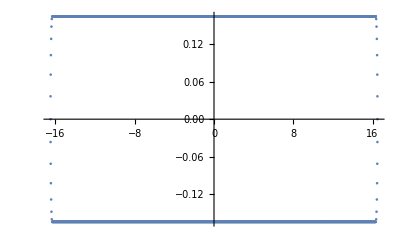

```mathematica
ListPlot[Pts]
```

```mathematica
Export["blasius"<>ToString[Length@Pts],
{"/*--------------------------------*- VM2D -*-----------------*---------------*\\
| ##  ## ##   ##  ####  #####   |                            | Version 1.11   |
| ##  ## ### ### ##  ## ##  ##  |  VM2D: Vortex Method       | 2022/08/07     |
| ##  ## ## # ##    ##  ##  ##  |  for 2D Flow Simulation    *----------------*
|  ####  ##   ##   ##   ##  ##  |  Open Source Code                           |
|   ##   ##   ## ###### #####   |  https://www.github.com/vortexmethods/VM2D  |
|                                                                             |
| Copyright (C) 2017-2022 Ilia Marchevsky, Kseniia Sokol, Evgeniya Ryatina    |
*-----------------------------------------------------------------------------*
| File name: Blasius"<>TextString[Length@Pts]<>StringRepeat[" ",58-StringLength@ToString[Length@Pts]]<>"|
| Info: Blasius airfoil ("<>TextString[Length@Pts]<>" panels)"<>StringRepeat[" ",45-StringLength@ToString[Length@Pts]]<>"|
\\*---------------------------------------------------------------------------*/
"}~Join~{"r = {"}~Join~((TextString[#]<>",")&/@(Pts[[1;;-2]]))~Join~((TextString[#])&/@(Pts[[{-1}]]))~Join~{" };"},"Table"]
```

blasius3556